Worksheet 2, Math 152      *      D. Maslanka         *     Fall 2015

INVERSE TRIGONOMETRIC FUNCTIONS & TRIG SUBSTITUTIONS

Goals:  In this worksheet we will use integration with Mathematica to:  
determine the area of a plane region, find the arclength of a curve, 
and compute the volume of a solid of revolution. 
  
Consider the function  f ( x )  =   arctan ((x-1)/(x+1))  for   -1 ⩽ x ⩽ 4.
We may sketch a graph of this function using Mathematica.

```mathematica
Clear[f]
f[x_]:=ArcTan[(x-1)/(x+1)]
"f(x)="f[x]
Plot[f[x],{x,-1,4},PlotStyle->{Darker[Blue],Thickness[0.003]},AxesLabel->{x,y}]
```

If we would like to add the name of the curve to the above plot, we may do so using 
a Text instruction which is included in Mathematica's Graphics package.

```mathematica
p1=Plot[f[x],{x,-1,4},PlotStyle->{Darker[Blue],Thickness[0.003]},Axes->True,AxesLabel->{x,y}];
t1=Graphics[Text[Style["y = arctan((x - 1)/(x + 1))",Bold,Italic,9,Darker[Red]],{1,0.45}]];
Show[p1,t1]
```

The area ( in square units ) of the region bounded between the graph 
of  f  and the x-axis, for    -1  ⩽ x ⩽ 4 ,  is given by

A=∫_-1^4 Abs[f(x)]ⅆx .

```mathematica
A=Integrate[Abs[f[x]],{x,-1,4}]
```

To ten significant digits, we find:

```mathematica
ApproximateArea=N[A,10]
```

In order to find the length  L  of the graph of   y = arctan ((x-1)/(x+1))  from
    ( -1 , ℼ/2 )  to   ( 4 ,  arctan(3/5)  ),   
we use the fact that, in general,

L=∫_a^b √(1+(dy/dx)^2)ⅆx

gives the arc length of that portion of the graph of  y =  f ( x )  
between the points ( a ,  f ( a ) )  and  ( b ,  f ( b ) ).
Therefore, we find that

```mathematica
L=Integrate[Sqrt[1+(f'[x])^2],{x,-1,4}]
```

Although Mathematica  has returned an expression involving elliptic functions, we 
can almost always obtain a numerical estimate of the integral using the  
NIntegrate  instruction.

```mathematica
ApproximateLength=NIntegrate[Sqrt[1+(f'[x])^2],{x,-1,4}]
```

Upon rotating the graph of  f  about the x-axis we obtain the solid, S, having a circular 
cross-section in the plane perpendicular to the  x-axis at x = c, (for each choice of  c  
between  -1 and  + 4 ). This circle is centered on the x-axis and has radius f ( c ).  It may 
be described by the following parametric equations for the variables  y  and  z :

                             y  =  f ( a ) cos θ  ,   z = f ( a ) sin θ         for  0  < θ  <  2ℼ  
                              
Parametric equations for plane curves are an important topic which will be thoroughly 
discussed later on in this course, so don't be concerned if this seems confusing now.
  
Thus, the solid  S  may be described as the following set of ordered triples in three-space:

          S = { ( x , y , z ) :  y = f ( x ) cos θ,  z = f ( x ) sin θ   for all  -1 < x < 4   and   0 ⩽ t ⩽ 2ℼ   }.

We now proceed to plot the solid using Mathematica.

```mathematica
f[x_]:=ArcTan[(x-1)/(x+1)]
ParametricPlot3D[{x,f[x]*Cos[θ],f[x]*Sin[θ]},{x,-1,4},{θ,0,2*π},PlotStyle->Opacity[0.5],AxesLabel->{x,y,z},ViewPoint->{2,-Pi/3,Pi/6}]
```

In order to animate the rotation of the graph of  y  =  f ( x )  about the  x - axis, execute the following
instruction. Then use your mouse to click on the  PLAY  button on the toolbar so that the rotation will proceed.

```mathematica
Animate[ParametricPlot3D[{x,f[x]*Cos[θ*t],f[x]*Sin[θ*t]},{x,-1,4},{θ,0,2*Pi},PlotStyle->Opacity[0.5],AxesLabel->{x,y,z},ViewPoint->{2,-Pi/3,Pi/6}],{t,0,1},AnimationRate->0.15,AnimationRepetitions->1,AnimationRunning->False]
```

The volume V enclosed by this solid of revolution is given by:

```mathematica
V=Integrate[Pi*(f[x])^2,{x,-1,4}]
```

The decimal value of this integral (in cubic units) is given by:

```mathematica
ApproxV=NIntegrate[Pi*(f[x])^2,{x,-1,4}]
```

_________________________________________________                          
Exercises
1.  Let  f ( x )  = x arctan ( 1/x ).

( a )  Define the function  f  in Mathematica and then plot its graph for   -ℼ/2 ⩽  x  ⩽ ℼ  .

```mathematica
f[x_]:=x ArcTan[1/x]
```

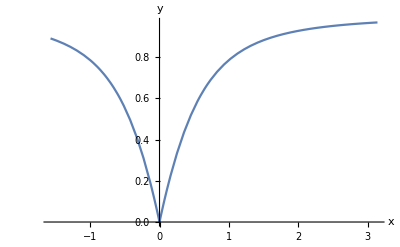

```mathematica
Plot[f[x],{x,-π/2,π},AxesLabel->{x,y}]
```

( b )  The region between the graph of   y = x arctan ( 1/x )    for  -ℼ/2 ⩽ x ⩽ ℼ  is rotated about
              the x-axis. Plot a three-dimensional graph of the resulting solid.

```mathematica
ParametricPlot3D[{x,f[x]*Cos[θ],f[x]*Sin[θ]},{x,-π/2,π},{θ,0,2*π},
PlotStyle->Opacity[0.5],AxesLabel->{x,y,z},ViewPoint->{2,-π/3,π/6}]
```

( c )  Use  Mathematica’s NIntegrate instruction (click on: NIntegrate for help) to obtain 
              a decimal approximation to the volume of the solid of revolution described in part ( b ).

```mathematica
vol = NIntegrate[π*f[x]^2,{x,-π/2,π}]
```

8.82145

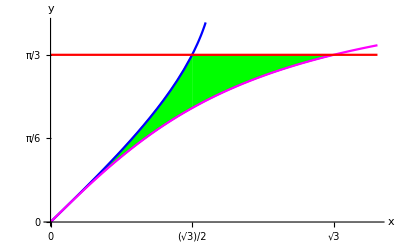
2.  ( a )  Use  Mathematica  to plot a graph of the region bounded by the curves:  y  =  arcsin x , 
              y  =  arctan x ,    and    y  = ℼ/3  .
             Your graph should resemble that shown below. 
                -Graphics-

To shade-in the bounded area, you should use the color and Filling options in your
              Plot instructions together with the Show instruction. 
              By executing the following sequence, the desired region bounded between the graphs of arcsine and 
              arctangent will appear in green. Now you just need to finish the shading!

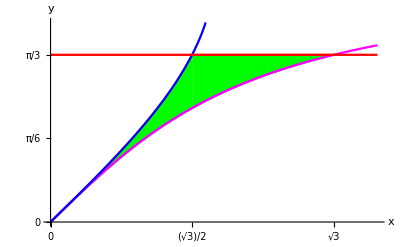

```mathematica
g1=Plot[ArcTan[x],{x,0,2},PlotRange->{0,1.25},PlotStyle->{Magenta,Thickness[0.004]}];g2=Plot[ArcSin[x],{x,0,2},PlotRange->{0,1.25},PlotStyle->{Blue,Thickness[0.004]}];
g3=Plot[π/3,{x,0,2},PlotRange->{0,1.25},PlotStyle->{Red,Thickness[0.004]}];
p1=Plot[{ArcTan[x],ArcSin[x]},{x,0,Sqrt[3]/2},Filling->{1->{{2},{Green}}},PlotRange->{{0,2},{0,1.25}}];
p2=Plot[{ArcTan[x],π/3},{x,Sqrt[3]/2,√3},Filling->{1->{{2},{Green}}},PlotRange->{{0,2},{0,1.25}}];
Show[p1,p2,g1,g2,g3,Ticks->{{0,Sqrt[3]/2,Sqrt[3]},{0,Pi/6,Pi/3}},AxesLabel->{x,y}]
```

( b )  Use  Mathematica to find the exact area of the shaded region. 
            (Hint: It is easiest to solve this problem by integrating with respect to y ).

```mathematica
a1 = Integrate[ArcSin[x],{x,0,(√3)/2}]-Integrate[ArcTan[x],{x,0,(√3)/2}];
a2 = Integrate[{π/3},{x,(√3)/2,√3}]-Integrate[ArcTan[x],{x,(√3)/2,√3}];
areaTotal = N[a1+a2]
```

{0.193147}

( c )  Use  Mathematica’s NIntegrate instruction and the  D instruction (click on  D  for more details) to 
            obtain a decimal approximation to the length of the boundary of the shaded region in the figure.

```mathematica
len1 = NIntegrate[√(1+D[ArcTan[x],x]^2),{x,0,√3}];
len2 = NIntegrate[√(1+D[ArcSin[x],x]^2),{x,0,(√3)/2}];
len3 = √3-(√3)/2;
lenTotal = len1+len2+len3
```

4.28767

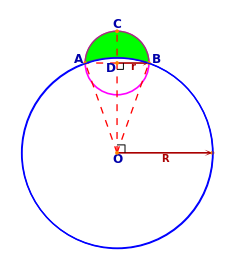
_________________________________________________           
  The green crescent shaped region bounded by circles of radii   r  and  R  displayed below 
  is called a  lune.
                              -Graphics-
                          
In problems  3  and  4  you will determine the area of the lune in two ways: first analytically using 
integration techniques with Mathematica and then geometrically using area formulas for triangles and 
sectors of circles.

_______________________________________________________ 

3.  Suppose that a Cartesian coordinate system is imposed on the plane so that point  O  lies at 
     the origin and point  D  lies along the positive  y - axis.
( a )  Determine the Mathematica formula for the function,  f ,  that describes the upper semicircle 
              of the large circle having radius  R  and center O .

```mathematica
ClearAll[x,y,r,R,f]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
(* (y-b)^2 = R^2-(x-a)^2 *)
(* y = √(R^2-(x-a)^2)+b *)
(* O = (a,b) = (0,0) *)
f[x_]:=√(R^2-x^2)
```

( b )  Determine the Mathematica formula for the function,  g ,  that describes the upper semicircle 
              of the small circle having radius  r  and with center  D .

```mathematica
Solve[x^2+(y-√(R^2-r^2))^2==r^2,y]
```

{{y→√(-r^2+R^2)-√(r^2-x^2)},{y→√(-r^2+R^2)+√(r^2-x^2)}}

```mathematica
g[x_]:=√(-r^2+R^2)+√(r^2-x^2)
```

( c )   Evaluate the Mathematica integral shown below in order to calculate the area of the lune,
             ( i.e., the green shaded region which is bounded above by the small circle and below by the larger one.)

```mathematica
Integrate[g[x]-f[x],{x,-r,r},Assumptions->{r>0,(R/r)>1}]
```

```mathematica
(π r^2)/2+r √(-r^2+R^2)-R^2 ArcTan[r/(√(-r^2+R^2))](** ArcTan[r/(√(-r^2+R^2))] == ArcSin[r/R] **)
```

( d )   Check the answer to parts ( c ) by computing the integral by hand. 
              Use a trigonometric substitution where necessary.

4.  ( a )  Use geometry to find the area of the semicircle through points A , B and C.

```mathematica
areaSemi = (π*r^2)/2
```

(π r^2)/2

( b )  Use right triangle trigonometry to find the  measure(∡ DOB )  in terms of  r  and  R.

```mathematica
angDOB = ArcSin[r/R]
```

ArcSin[r/R]

( c )  Now find the area of sector  AOB . 
             Note:  measure( ∡ AOB ) =  2 × measure( ∡ DOB ) .

```mathematica
areaAOB = R^2×π×((2angDOB)/(2π))
```

R^2 ArcSin[r/R]

( d )  Find the area of △ AOB .  Note:  Area ( △ AOB )  =  r × | OD | .

```mathematica
areaTriAOB = r×R×Cos[angDOB]
```

r √(1-r^2/R^2) R

( e )  From parts  ( a ) , ( c ) , and ( d )  determine the area of the lune.

```mathematica
luneArea = areaSemi-areaAOB- areaTriAOB
```

(π r^2)/2-r √(1-r^2/R^2) R-R^2 ArcSin[r/R]

```mathematica
(** ArcTan[r/(√(-r^2+R^2))] == ArcSin[r/R] **)
```